```mathematica
V= 0.5*x[t]^2-0.5*x[t]^3+0.96/8*x[t]^4
```

0.5 x[t]^2-0.5 x[t]^3+0.12 x[t]^4

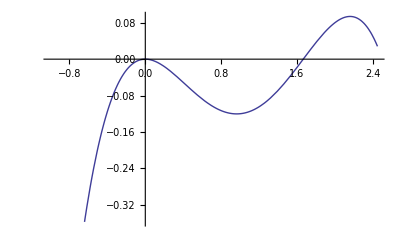

```mathematica
Plot[-V,{x[t],-1,2.45}]
```

```mathematica
FindRoot[V,{x[t],1.5}]
```

{x[t]→1.66667}

```mathematica
sol1 = NDSolve[{D[V,x[t]]-x''[t]-x'[t]/t  ==0,x[0.0000000001]== 2.15992237,x'[0.0000000001]==0},x,{t,0.0001,100}]
```

{{x→InterpolatingFunction[{{0.0001,100.}},<>]}}

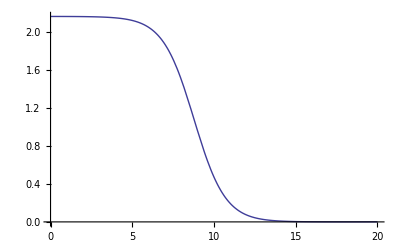

```mathematica
Plot[x[t] /. sol1, {t,0,20}]
```

```mathematica
3
```

```mathematica
table= Table[x[t] /. sol1,{t,0,20,20/4001}]
```

{{2.15992},{2.15992},{2.15992},{2.15992},{2.15992},{2.15992},«3990»,{0.000600294},{0.000603025},{0.000605769},{0.000608529},{0.000611303},{0.000614091}}

```mathematica
Export[FileNameJoin[{$HomeDirectory,"file_in.txt"}],table,"TSV"]
```

/Users/matthewcitron/file_in.txt